```mathematica
2-2
```

0

```mathematica
Subscript[σ, 0]=({{1, 0}, {0, 1}});
Subscript[σ, 1]=({{0, 1}, {1, 0}});
Subscript[σ, 2]=({{0, -ⅈ}, {ⅈ, 0}});
Subscript[σ, 3]=({{1, 0}, {0, -1}});

Comm[x_,y_]:=x.y-y.x

Subscript[𝕆, 2]=({{0, 0}, {0, 0}});
Subscript[𝕆, 3]=({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}});
Subscript[𝕆, 4]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
DotProd[x_,y_]:=(Transpose[x].y)⟦1⟧⟦1⟧
```

```mathematica
Asher Peres' simplified proof of the KS Theorem
```

Nicholas Wheeler
Reed College Physics Department
22 March 2010

### Spin one-half preliminaries

The following 2×2 matrices are found to possess all the properties we expect of spin matrices in the case of spin one-half:

```mathematica
Subscript[𝕤, 1]=(ℏ/2)Subscript[σ, 1];
Subscript[𝕤, 2]=(ℏ/2)Subscript[σ, 2];
Subscript[𝕤, 3]=(ℏ/2)Subscript[σ, 3];
```

```mathematica
Eigenvalues[Subscript[𝕤, 1]]
Eigenvalues[Subscript[𝕤, 2]]
Eigenvalues[Subscript[𝕤, 3]]
```

{-ℏ/2,ℏ/2}

{-ℏ/2,ℏ/2}

{-ℏ/2,ℏ/2}

```mathematica
m ℏ/.m->±1/2
```

1/2 ℏ (±1)

```mathematica
Eigenvalues[Subscript[𝕤, 1].Subscript[𝕤, 1]+Subscript[𝕤, 2].Subscript[𝕤, 2]+Subscript[𝕤, 3].Subscript[𝕤, 3]]
```

{(3 ℏ^2)/4,(3 ℏ^2)/4}

```mathematica
ℏ^2 ℓ(ℓ+1)/.ℓ->1/2
```

(3 ℏ^2)/4

We find that if we measure spin in the direction defined by the unit vector x⃗ we get the same result for all directions

```mathematica
𝕩=Subscript[x, 1] Subscript[𝕤, 1]+Subscript[x, 2] Subscript[𝕤, 2]+Subscript[x, 3] Subscript[𝕤, 3];
𝕪=Subscript[y, 1] Subscript[𝕤, 1]+Subscript[y, 2] Subscript[𝕤, 2]+Subscript[y, 3] Subscript[𝕤, 3];
```

```mathematica
Assuming[Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2==1,Simplify[𝕩.𝕩]]//MatrixForm
```

(ℏ^2/4 | 0
0 | ℏ^2/4)

—this because

```mathematica
{-ℏ/2,ℏ/2}^2
```

{ℏ^2/4,ℏ^2/4}

And we find, moveover, that—trivially—all such measurements commute:

```mathematica
Comm[𝕩.𝕩,𝕪.𝕪]==Subscript[𝕆, 2]
```

True

```mathematica
Assuming[Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2==1,Simplify[Eigenvalues[𝕩.𝕩]]]
```

{ℏ^2/4,ℏ^2/4}

### A remarkable property of spin-one particles: the 110 principle

The situation is now similar in many respects, but more interesting:

```mathematica
Subscript[𝕤, 1]=.
Subscript[𝕤, 2]=.
Subscript[𝕤, 3]=.
```

```mathematica
Clear[𝕩,𝕪]
```

```mathematica
Subscript[𝕤, 1]=ℏ({{0, 0, 0}, {0, 0, -ⅈ}, {0, ⅈ, 0}});
Subscript[𝕤, 2]=ℏ({{0, 0, ⅈ}, {0, 0, 0}, {-ⅈ, 0, 0}});
Subscript[𝕤, 3]=ℏ({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 0}});
```

```mathematica
Comm[Subscript[𝕤, 1],Subscript[𝕤, 2]]==ⅈ ℏ Subscript[𝕤, 3]
Comm[Subscript[𝕤, 2],Subscript[𝕤, 3]]==ⅈ ℏ Subscript[𝕤, 1]
Comm[Subscript[𝕤, 3],Subscript[𝕤, 1]]==ⅈ ℏ Subscript[𝕤, 2]
```

True

True

True

```mathematica
𝕊𝕊=Subscript[𝕤, 1].Subscript[𝕤, 1]+Subscript[𝕤, 2].Subscript[𝕤, 2]+Subscript[𝕤, 3].Subscript[𝕤, 3];
```

```mathematica
Comm[𝕊𝕊,Subscript[𝕤, 1]]==Subscript[𝕆, 3]
Comm[𝕊𝕊,Subscript[𝕤, 2]]==Subscript[𝕆, 3]
Comm[𝕊𝕊,Subscript[𝕤, 3]]==Subscript[𝕆, 3]
```

True

True

True

```mathematica
Eigenvalues[Subscript[𝕤, 1]]
Eigenvalues[Subscript[𝕤, 2]]
Eigenvalues[Subscript[𝕤, 3]]
```

{0,-ℏ,ℏ}

{0,-ℏ,ℏ}

{0,-ℏ,ℏ}

```mathematica
Eigenvalues[𝕊𝕊]
```

{2 ℏ^2,2 ℏ^2,2 ℏ^2}

Spin measurements in directions x⃗ and y⃗ are found now to commute if and only if the directions are perpendicular:

```mathematica
𝕩=Subscript[x, 1] Subscript[𝕤, 1]+Subscript[x, 2] Subscript[𝕤, 2]+Subscript[x, 3] Subscript[𝕤, 3];
𝕪=Subscript[y, 1] Subscript[𝕤, 1]+Subscript[y, 2] Subscript[𝕤, 2]+Subscript[y, 3] Subscript[𝕤, 3];
𝕫=Subscript[z, 1] Subscript[𝕤, 1]+Subscript[z, 2] Subscript[𝕤, 2]+Subscript[z, 3] Subscript[𝕤, 3];
```

```mathematica
Assuming[{Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2==1,Subscript[y, 1]^2+Subscript[y, 2]^2+Subscript[y, 3]^2==1},Simplify[Comm[𝕩.𝕩,𝕪.𝕪]]]//MatrixForm
```

(0 | ℏ^4 (-x_2 y_1+x_1 y_2) (x_1 y_1+x_2 y_2+x_3 y_3) | ℏ^4 (-x_3 y_1+x_1 y_3) (x_1 y_1+x_2 y_2+x_3 y_3)
ℏ^4 (x_2 y_1-x_1 y_2) (x_1 y_1+x_2 y_2+x_3 y_3) | 0 | -ℏ^4 (x_3 y_2-x_2 y_3) (x_1 y_1+x_2 y_2+x_3 y_3)
ℏ^4 (x_3 y_1-x_1 y_3) (x_1 y_1+x_2 y_2+x_3 y_3) | ℏ^4 (x_3 y_2-x_2 y_3) (x_1 y_1+x_2 y_2+x_3 y_3) | 0)

```mathematica
Assuming[{Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2==1,Subscript[y, 1]^2+Subscript[y, 2]^2+Subscript[y, 3]^2==1,Subscript[x, 1] Subscript[y, 1]+Subscript[x, 2] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 3]==0},Simplify[Comm[𝕩.𝕩,𝕪.𝕪]]]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

If we measure not spin but spin squared

```mathematica
Assuming[Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2==1,Simplify[Eigenvalues[𝕩.𝕩]]]
Assuming[Subscript[y, 1]^2+Subscript[y, 2]^2+Subscript[y, 3]^2==1,Simplify[Eigenvalues[𝕪.𝕪]]]
Assuming[Subscript[z, 1]^2+Subscript[z, 2]^2+Subscript[z, 3]^2==1,Simplify[Eigenvalues[𝕫.𝕫]]]
```

{0,ℏ^2,ℏ^2}

{0,ℏ^2,ℏ^2}

{0,ℏ^2,ℏ^2}

```mathematica
Assuming[{Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2==1,Subscript[y, 1]^2+Subscript[y, 2]^2+Subscript[y, 3]^2==1,Subscript[z, 1]^2+Subscript[z, 2]^2+Subscript[z, 3]^2==1,Subscript[x, 1] Subscript[y, 1]+Subscript[x, 2] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 3]==0,Subscript[x, 1] Subscript[z, 1]+Subscript[x, 2] Subscript[z, 2]+Subscript[x, 3] Subscript[z, 3]==0,Subscript[y, 1] Subscript[z, 1]+Subscript[y, 2] Subscript[z, 2]+Subscript[y, 3] Subscript[z, 3]==0},Simplify[𝕩.𝕩+𝕪.𝕪+𝕫.𝕫]]
```

{{2 ℏ^2,0,0},{0,2 ℏ^2,0},{0,0,2 ℏ^2}}

```mathematica
Eigenvalues[%]
```

{2 ℏ^2,2 ℏ^2,2 ℏ^2}

we discover that in every case two meters register ℏ^2 while the third registers 0. We have encountered here the "110 principle", upon which all subsequent argument hinges.

Looking back in this light to the theory of spin one-half particles, we encounter a "111 principle," which is trivially uninformative. Looking ahead to the theory of spin three-halves particles, we have

```mathematica
Subscript[𝕤, 1]=.
Subscript[𝕤, 2]=.
Subscript[𝕤, 3]=.
Clear[𝕊𝕊,𝕩,𝕪,𝕫]
```

```mathematica
Clear
```

```mathematica
Subscript[𝕤, 1]=ℏ/2({{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}});
Subscript[𝕤, 2]=ⅈ ℏ/2({{0, -√3, 0, 0}, {√3, 0, -2, 0}, {0, 2, 0, -√3}, {0, 0, √3, 0}});
Subscript[𝕤, 3]=ℏ/2({{3, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -3}});
```

```mathematica
Comm[Subscript[𝕤, 1],Subscript[𝕤, 2]]==ⅈ ℏ Subscript[𝕤, 3]//Simplify
Comm[Subscript[𝕤, 2],Subscript[𝕤, 3]]==ⅈ ℏ Subscript[𝕤, 1]//Simplify
Comm[Subscript[𝕤, 3],Subscript[𝕤, 1]]==ⅈ ℏ Subscript[𝕤, 2]//Simplify
```

True

True

True

```mathematica
𝕊𝕊=Subscript[𝕤, 1].Subscript[𝕤, 1]+Subscript[𝕤, 2].Subscript[𝕤, 2]+Subscript[𝕤, 3].Subscript[𝕤, 3];
```

```mathematica
Comm[𝕊𝕊,Subscript[𝕤, 1]]==Subscript[𝕆, 4]
Comm[𝕊𝕊,Subscript[𝕤, 2]]==Subscript[𝕆, 4]
Comm[𝕊𝕊,Subscript[𝕤, 3]]==Subscript[𝕆, 4]
```

True

True

True

```mathematica
Eigenvalues[Subscript[𝕤, 1]]
Eigenvalues[Subscript[𝕤, 2]]
Eigenvalues[Subscript[𝕤, 3]]
```

{-(3 ℏ)/2,-ℏ/2,ℏ/2,(3 ℏ)/2}

{-(3 ℏ)/2,-ℏ/2,ℏ/2,(3 ℏ)/2}

{-(3 ℏ)/2,-ℏ/2,ℏ/2,(3 ℏ)/2}

```mathematica
Eigenvalues[𝕊𝕊]
```

{(15 ℏ^2)/4,(15 ℏ^2)/4,(15 ℏ^2)/4,(15 ℏ^2)/4}

```mathematica
ℏ^2 ℓ(ℓ+1)/.ℓ->3/2
```

(15 ℏ^2)/4

```mathematica
Assuming[ℏ≠0,Simplify[Comm[Subscript[𝕤, 1].Subscript[𝕤, 1],Subscript[𝕤, 2].Subscript[𝕤, 2]]==Subscript[𝕆, 4]]]
Assuming[ℏ≠0,Simplify[Comm[Subscript[𝕤, 2].Subscript[𝕤, 2],Subscript[𝕤, 3].Subscript[𝕤, 3]]==Subscript[𝕆, 4]]]
Assuming[ℏ≠0,Simplify[Comm[Subscript[𝕤, 3].Subscript[𝕤, 3],Subscript[𝕤, 1].Subscript[𝕤, 1]]==Subscript[𝕆, 4]]]
```

False

False

False

we discover that now spin-squared matrices do not commute. We encounter a brick wall even before we can contemplate phrasing an analog of the 110 principle. And so it goes also for all higher spin-values.

### Enter: The (non-contextual) hidden variable hypothesis

To account for 110-property of spin-one particles, we posit the existence of "instruction sets" (inscribed on "hidden variables") that tell the particle to register 1 else 0 when subjected to a spin-squared measurement, and that those instructions are so coordinated that two members of every orthogonal triad are painted blue (instructed to register 1) and one member is painted red (instructed to register 0).

-Graphics3D-

In 1967, Simon Kochen & Ernst Specker

```mathematica
Hyperlink["Kocken-Specker 1","http://en.wikipedia.org/wiki/Kochen-Specker_theorem"]
```

```mathematica
Hyperlink["Kochen-Specker 2","http://plato.stanford.edu/entries/kochen-specker/"]
```

constructed a finite system of orthogonal tetrads for which compliance with the 110 principle could be shown to pose an insoluable combinatorial problem. Their system was constructed from a set of 117 lines (rays) derived (how God only knows) from the following famous diagram:

In 1991, Asher Peres produced a simplification of the Kochen-Specker argument that made use of only 33 rays:

-Graphics3D-

We are not told how Peres arrived at that set of rays. Roger Penrose observed that they can be obtained as symmetry axes of the following figure

-Graphics3D-

which appears in Escher's "The Waterfall" (which was based upon an idea supplied to Escher by Penrose's father):

The figure supports three distinct classes of triad:

-Graphics3D-

-Graphics3D-

### Peres' set of 33 rays

From Penrose's construction leads to this construction of 39 rays

```mathematica
Clear[α,β,γ]
```

```mathematica
r=√2;
Subscript[α, 1]={{r},{1},{1}};
Subscript[α, 2]={{r},{0},{1}};
Subscript[α, 3]={{r},{-1},{1}};
Subscript[α, 4]={{r},{1},{0}};
Subscript[α, 5]={{r},{0},{0}};
Subscript[α, 6]={{r},{-1},{0}};
Subscript[α, 7]={{r},{1},{-1}};
Subscript[α, 8]={{r},{0},{-1}};
Subscript[α, 9]={{r},{-1},{-1}};
Subscript[α, 10]={{r},{r},{0}};
Subscript[α, 11]={{r},{-r},{0}};
Subscript[α, 12]={{r},{0},{r}};
Subscript[α, 13]={{r},{0},{-r}};
Table[Subscript[β, k]=({{0, 0, -1}, {0, 1, 0}, {1, 0, 0}}).Subscript[α, k],{k,1,13}];

Table[Subscript[γ, k]=({{1, 0, 0}, {0, 0, -1}, {0, 1, 0}}).Subscript[β, k],{k,1,13}];
```

of which three, however, have been given multiple names

```mathematica
Count[Flatten[Table[Subscript[α, j]==Subscript[β, k],{j,1,13},{k,1,13}]],True]
Count[Flatten[Table[Subscript[α, j]==Subscript[γ, k],{j,1,13},{k,1,13}]],True]
Count[Flatten[Table[Subscript[β, j]==Subscript[γ, k],{j,1,13},{k,1,13}]],True]
```

1

1

1

Specifically,

```mathematica
Subscript[α, 12]==Subscript[β, 13]
Subscript[α, 11]==Subscript[γ, 13]
Subscript[β, 11]==Subscript[γ, 10]
```

True

True

True

Normalizing the 39 α/β/γ vectors and taking those identifications into account, we arrive at a list of

```mathematica
9+9+9+6
```

33

unit vectors (rays)

```mathematica
Table[Subscript[a, k]=Subscript[α, k]/Norm[Subscript[α, k]],{k,1,13}];
Table[Subscript[b, k]=Subscript[β, k]/Norm[Subscript[β, k]],{k,1,13}];
Table[Subscript[c, k]=Subscript[γ, k]/Norm[Subscript[γ, k]],{k,1,13}];
Subscript[x, 1]=Subscript[a, 10];
Subscript[x, 2]=Subscript[a, 11];
Subscript[x, 3]=Subscript[a, 12];
Subscript[x, 4]=Subscript[a, 13];
Subscript[x, 5]=Subscript[b, 10];
Subscript[x, 6]=Subscript[b, 11];
```

to which I now give unified names:

```mathematica
Subscript[R, 1]=Subscript[a, 1];
Subscript[R, 2]=Subscript[a, 2];
Subscript[R, 3]=Subscript[a, 3];
Subscript[R, 4]=Subscript[a, 4];
Subscript[R, 5]=Subscript[a, 5];
Subscript[R, 6]=Subscript[a, 6];
Subscript[R, 7]=Subscript[a, 7];
Subscript[R, 8]=Subscript[a, 8];
Subscript[R, 9]=Subscript[a, 9];
Subscript[R, 10]=Subscript[b, 1];
Subscript[R, 11]=Subscript[b, 2];
Subscript[R, 12]=Subscript[b, 3];
Subscript[R, 13]=Subscript[b, 4];
Subscript[R, 14]=Subscript[b, 5];
Subscript[R, 15]=Subscript[b, 6];
Subscript[R, 16]=Subscript[b, 7];
Subscript[R, 17]=Subscript[b, 8];
Subscript[R, 18]=Subscript[b, 9];
Subscript[R, 19]=Subscript[c, 1];
Subscript[R, 20]=Subscript[c, 2];
Subscript[R, 21]=Subscript[c, 3];
Subscript[R, 22]=Subscript[c, 4];
Subscript[R, 23]=Subscript[c, 5];
Subscript[R, 24]=Subscript[c, 6];
Subscript[R, 25]=Subscript[c, 7];
Subscript[R, 26]=Subscript[c, 8];
Subscript[R, 27]=Subscript[c, 9];
Subscript[R, 28]=Subscript[x, 1];
Subscript[R, 29]=Subscript[x, 2];
Subscript[R, 30]=Subscript[x, 3];
Subscript[R, 31]=Subscript[x, 4];
Subscript[R, 32]=Subscript[x, 5];
Subscript[R, 33]=Subscript[x, 6];
```

### Identification of orthogonal pairs of Peres rays

Peres rays can be taken in

```mathematica
Binomial[33,2]
```

528

distinct pairwise combinations. From

```mathematica
Count[Flatten[Table[DotProd[Subscript[R, i],Subscript[R, j]],{i,1,32},{j,i+1,33}]],0]
```

72

we see that there are a total of 72 orthogonal pairs or Peres rays. To discover their identities, we proceed

```mathematica
NamedPair[i_,j_]:={{DotProd[Subscript[R, i],Subscript[R, j]]},{i,j}}
```

```mathematica
MasterPairList=Flatten[Table[NamedPair[i,j],{i,1,32},{j,i+1,33}],1];
```

```mathematica
Length[%]
```

528

```mathematica
OrthogonalPairSearch=Table[If[MasterPairList⟦k⟧⟦1⟧=={0},MasterPairList⟦k⟧⟦2⟧],{k,1,528}];
```

The beginning of that long list looks like this:

```mathematica
Take[%,50]
```

{Null,Null,Null,Null,Null,Null,Null,{1,9},Null,{1,11},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{1,26},Null,Null,Null,Null,Null,Null,{1,33},Null,Null,Null,Null,Null,Null,Null,{2,10},{2,11},{2,12},Null,Null,Null,Null,Null,Null,Null,Null}

We (by hand!) erase all the Nulls, and obtain this named list of orthogonal pairs of Peres rays:

```mathematica
OrthogonalPairs={{1,9},{1,11},{1,26},{1,33},{2,10},{2,11},{2,12},{2,23},{3,7},{3,11},{3,20},{3,32},{4,14},{4,25},{4,26},{4,27},{5,13},{5,14},{5,15},{5,22},{5,23},{5,24},{5,32},{5,33},{6,14},{6,19},{6,20},{6,21},{7,17},{7,26},{7,32},{8,16},{8,17},{8,18},{8,23},{9,17},{9,20},{9,33},{10,18},{10,22},{10,28},{11,23},{12,16},{12,24},{12,29},{13,19},{13,22},{13,25},{14,20},{14,23},{14,26},{14,28},{14,29},{15,21},{15,24},{15,27},{16,22},{16,29},{17,23},{18,24},{18,28},{19,27},{19,30},{21,25},{21,31},{23,30},{23,31},{25,31},{27,30},{28,29},{30,31},{32,33}};
```

```mathematica
Length[OrthogonalPairs]
```

72

We will have need of this list later in the discussion. For the moment is useful mainly as methodological guidance when we turn to construction of a named list of orthogonal triads:

### Identification of orthogonal triads

Peres rays can be taken in

```mathematica
Binomial[33,3]
```

5456

distinct triadic combinations. From

```mathematica
Triad[i_,j_,k_]:={DotProd[Subscript[R, i],Subscript[R, j]],DotProd[Subscript[R, i],Subscript[R, k]],DotProd[Subscript[R, k],Subscript[R, j]]}
```

```mathematica
Count[Flatten[Table[Triad[i,j,k],{i,1,31},{j,i+1,32},{k,j+1,33}],2],{0,0,0}]
```

16

we see that only 16 (only 0.29%) comprise orthogonal triads. To discover those (and their names) we proceed very much as before:

```mathematica
Flatten[Table[{DotProd[Subscript[R, i],Subscript[R, j]],DotProd[Subscript[R, i],Subscript[R, k]],DotProd[Subscript[R, k],Subscript[R, j]]},{i,1,31},{j,i+1,32},{k,j+1,33}],2];
```

```mathematica
NamedTriad[i_,j_,k_]:={{DotProd[Subscript[R, i],Subscript[R, j]],DotProd[Subscript[R, i],Subscript[R, k]],DotProd[Subscript[R, k],Subscript[R, j]]},{i,j,k}}
```

```mathematica
MasterTriadList=Flatten[Table[NamedTriad[i,j,k],{i,1,31},{j,i+1,32},{k,j+1,33}],2];
```

```mathematica
Length[MasterTriadList]
```

5456

```mathematica
OrthogonalTriadSearch=Table[If[MasterTriadList⟦k⟧⟦1⟧=={0,0,0},MasterTriadList⟦k⟧⟦2⟧],{k,1,5456}];
```

I show a small portion of that very long list:

```mathematica
Take[OrthogonalTriadSearch,{200,300}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{1,9,33},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Removing (by hand!!) all the Nulls, we obtain

```mathematica
OrthogonalTriads={{1,9,33},{2,11,23},{3,7,32},{4,14,26},{5,13,22},{5,14,23},{5,15,24},{5,32,33},{6,14,20},{8,17,23},{10,18,28},{12,16,29},{14,28,29},{19,27,30},{21,25,31},{23,30,31}};
```

```mathematica
Length[OrthogonalTriads]
```

16

From

```mathematica
Table[Count[Flatten[OrthogonalTriads],k],{k,1,33}]
```

{1,1,1,1,4,1,1,1,1,1,1,1,1,4,1,1,1,1,1,1,1,1,4,1,1,1,1,2,2,2,2,2,2}

we see that most rays appear in only a single triad, but three are members simultaneously of 4 triads, while six are members simultaneously of 2 triads. As per the following diagram:

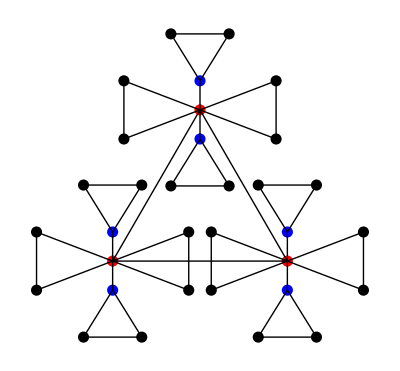

The three red dots refer to center-of-face rays, the six blue dots to center of edge rays.

### Lists of companions

To discover the identities of the rays that share triad membership with (say) R_5 we proceed

```mathematica
Table[If[Intersection[Part[OrthogonalTriads,j],{5}]≠{},Part[OrthogonalTriads,j],{}],{j,1,16}]
```

{{},{},{},{},{5,13,22},{5,14,23},{5,15,24},{5,32,33},{},{},{},{},{},{},{},{}}

```mathematica
Flatten[%]
```

{5,13,22,5,14,23,5,15,24,5,32,33}

```mathematica
DeleteDuplicates[%]
```

{5,13,22,14,23,15,24,32,33}

```mathematica
DeleteCases[%,5]
```

{13,22,14,23,15,24,32,33}

```mathematica
Sort[%]
```

{13,14,15,22,23,24,32,33}

I conflate that sequence of commands to construct "companions lists" for each of Peres' 33 rays:

```mathematica
CompanionsList=Table[Sort[
DeleteCases[
DeleteDuplicates[Flatten[Table[If[Intersection[Part[OrthogonalTriads,j],{k}]≠{},Part[OrthogonalTriads,j],{}],{j,1,16}]]],
k]],{k,1,33}]
```

{{9,33},{11,23},{7,32},{14,26},{13,14,15,22,23,24,32,33},{14,20},{3,32},{17,23},{1,33},{18,28},{2,23},{16,29},{5,22},{4,5,6,20,23,26,28,29},{5,24},{12,29},{8,23},{10,28},{27,30},{6,14},{25,31},{5,13},{2,5,8,11,14,17,30,31},{5,15},{21,31},{4,14},{19,30},{10,14,18,29},{12,14,16,28},{19,23,27,31},{21,23,25,30},{3,5,7,33},{1,5,9,32}}

```mathematica
Length[%]
```

33

From

```mathematica
Table[Count[Flatten[CompanionsList],k],{k,1,33}]
```

{2,2,2,2,8,2,2,2,2,2,2,2,2,8,2,2,2,2,2,2,2,2,8,2,2,2,2,4,4,4,4,4,4}

we see that three rays have 8 companions, six have 4 companions, the rest have only 2. The following list indicates how many companions each specific ray has:

```mathematica
Table[{k,Count[Flatten[CompanionsList],k]},{k,1,33}]
```

{{1,2},{2,2},{3,2},{4,2},{5,8},{6,2},{7,2},{8,2},{9,2},{10,2},{11,2},{12,2},{13,2},{14,8},{15,2},{16,2},{17,2},{18,2},{19,2},{20,2},{21,2},{22,2},{23,8},{24,2},{25,2},{26,2},{27,2},{28,4},{29,4},{30,4},{31,4},{32,4},{33,4}}

I use that information to define a "number of companions" function of ray-name:

```mathematica
Companions[k_]:=Part[CompanionsList,k]
```

### Attempts to paint triads in conformity with the 110 principle

This looks like a solution of the ray-painting problem:

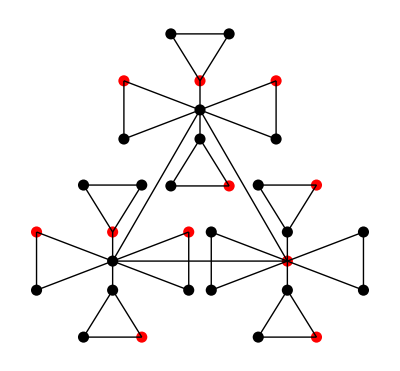

But is it? We attach appropriate ray-names to the dots

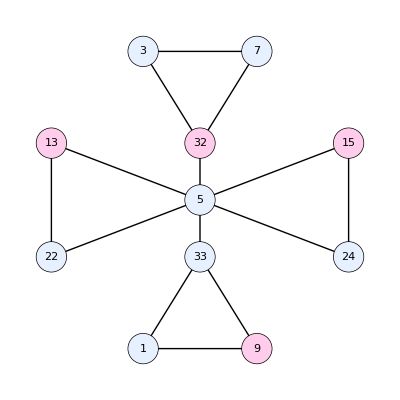

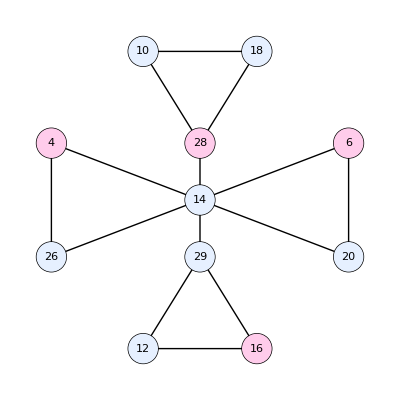

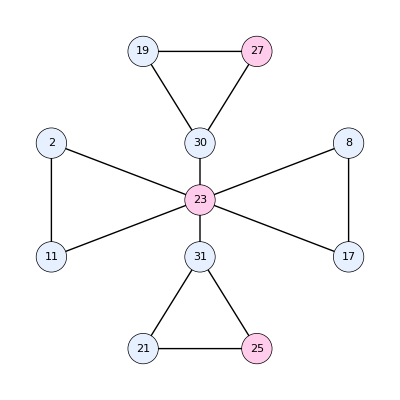

and list the rays we propose to paint red:

```mathematica
RedRays=Sort[{13,32,15,9,4,28,6,16,27,23,25}]
```

{4,6,9,13,15,16,23,25,27,28,32}

```mathematica
Length[RedRays]
```

11

I define a "paint" function, which paints a designated ray □ and its companions (wherever they occur) ■, in accordance with the 110 principle:

```mathematica
Paint[n_]:=Union[{n->□},Table[Part[Companions[n],j]->■,{j,1,Length[Companions[n]]}]]
```

and proceed to paint rays in the RedRays sequence:

```mathematica
OrthogonalTriads/.Paint[RedRays⟦1⟧]
```

{{1,9,33},{2,11,23},{3,7,32},{□,■,■},{5,13,22},{5,■,23},{5,15,24},{5,32,33},{6,■,20},{8,17,23},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{23,30,31}}

```mathematica
%/.Paint[RedRays⟦2⟧]
```

```mathematica
%/.Paint[RedRays⟦3⟧]
```

{{■,□,■},{2,11,23},{3,7,32},{□,■,■},{5,13,22},{5,■,23},{5,15,24},{5,32,■},{□,■,■},{8,17,23},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{23,30,31}}

```mathematica
%/.Paint[RedRays⟦4⟧]
```

{{■,□,■},{2,11,23},{3,7,32},{□,■,■},{■,□,■},{■,■,23},{■,15,24},{■,32,■},{□,■,■},{8,17,23},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{23,30,31}}

```mathematica
%/.Paint[RedRays⟦5⟧]
```

{{■,□,■},{2,11,23},{3,7,32},{□,■,■},{■,□,■},{■,■,23},{■,□,■},{■,32,■},{□,■,■},{8,17,23},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{23,30,31}}

```mathematica
%/.Paint[RedRays⟦6⟧]
```

{{■,□,■},{2,11,23},{3,7,32},{□,■,■},{■,□,■},{■,■,23},{■,□,■},{■,32,■},{□,■,■},{8,17,23},{10,18,28},{■,□,■},{■,28,■},{19,27,30},{21,25,31},{23,30,31}}

```mathematica
%/.Paint[RedRays⟦7⟧]
```

{{■,□,■},{■,■,□},{3,7,32},{□,■,■},{■,□,■},{■,■,□},{■,□,■},{■,32,■},{□,■,■},{■,■,□},{10,18,28},{■,□,■},{■,28,■},{19,27,■},{21,25,■},{□,■,■}}

```mathematica
%/.Paint[RedRays⟦8⟧]
```

{{■,□,■},{■,■,□},{3,7,32},{□,■,■},{■,□,■},{■,■,□},{■,□,■},{■,32,■},{□,■,■},{■,■,□},{10,18,28},{■,□,■},{■,28,■},{19,27,■},{■,□,■},{□,■,■}}

```mathematica
%/.Paint[RedRays⟦9⟧]
```

{{■,□,■},{■,■,□},{3,7,32},{□,■,■},{■,□,■},{■,■,□},{■,□,■},{■,32,■},{□,■,■},{■,■,□},{10,18,28},{■,□,■},{■,28,■},{■,□,■},{■,□,■},{□,■,■}}

```mathematica
%/.Paint[RedRays⟦10⟧]
```

{{■,□,■},{■,■,□},{3,7,32},{□,■,■},{■,□,■},{■,■,□},{■,□,■},{■,32,■},{□,■,■},{■,■,□},{■,■,□},{■,□,■},{■,□,■},{■,□,■},{■,□,■},{□,■,■}}

```mathematica
%/.Paint[RedRays⟦11⟧]
```

{{■,□,■},{■,■,□},{■,■,□},{□,■,■},{■,□,■},{■,■,□},{■,□,■},{■,□,■},{□,■,■},{■,■,□},{■,■,□},{■,□,■},{■,□,■},{■,□,■},{■,□,■},{□,■,■}}

It looks like we have succeeded!! BUT…look what we have done to the orthogonal pairs: recalling our instructions

```mathematica
RedRays
```

{4,6,9,13,15,16,23,25,27,28,32}

and their effect

```mathematica
Table[RedRays⟦k⟧->■,{k,1,Length[RedRays]}]
```

{4→■,6→■,9→■,13→■,15→■,16→■,23→■,25→■,27→■,28→■,32→■}

we have

```mathematica
Table[OrthogonalPairs⟦j⟧,{j,1,72}]/.Table[RedRays⟦k⟧->■,{k,1,Length[RedRays]}]
```

{{1,■},{1,11},{1,26},{1,33},{2,10},{2,11},{2,12},{2,■},{3,7},{3,11},{3,20},{3,■},{■,14},{■,■},{■,26},{■,■},{5,■},{5,14},{5,■},{5,22},{5,■},{5,24},{5,■},{5,33},{■,14},{■,19},{■,20},{■,21},{7,17},{7,26},{7,■},{8,■},{8,17},{8,18},{8,■},{■,17},{■,20},{■,33},{10,18},{10,22},{10,■},{11,■},{12,■},{12,24},{12,29},{■,19},{■,22},{■,■},{14,20},{14,■},{14,26},{14,■},{14,29},{■,21},{■,24},{■,■},{■,22},{■,29},{17,■},{18,24},{18,■},{19,■},{19,30},{21,■},{21,31},{■,30},{■,31},{■,31},{■,30},{■,29},{30,31},{■,33}}

On 4 occasions

```mathematica
Count[%,{■,■}]
```

4

we have painted orthogonal rays red, which the 110 principle disallows.

### An alternative failure

Suppose we start with the original orthogonal triad list

```mathematica
OrthogonalTriads
```

{{1,9,33},{2,11,23},{3,7,32},{4,14,26},{5,13,22},{5,14,23},{5,15,24},{5,32,33},{6,14,20},{8,17,23},{10,18,28},{12,16,29},{14,28,29},{19,27,30},{21,25,31},{23,30,31}}

and proceed by painting red the next yet-unpainted ray: we then achieve

```mathematica
OrthogonalTriads/.Paint[1]
```

{{□,■,■},{2,11,23},{3,7,32},{4,14,26},{5,13,22},{5,14,23},{5,15,24},{5,32,■},{6,14,20},{8,17,23},{10,18,28},{12,16,29},{14,28,29},{19,27,30},{21,25,31},{23,30,31}}

```mathematica
%/.Paint[2]
```

{{□,■,■},{□,■,■},{3,7,32},{4,14,26},{5,13,22},{5,14,■},{5,15,24},{5,32,■},{6,14,20},{8,17,■},{10,18,28},{12,16,29},{14,28,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[3]
```

{{□,■,■},{□,■,■},{□,■,■},{4,14,26},{5,13,22},{5,14,■},{5,15,24},{5,■,■},{6,14,20},{8,17,■},{10,18,28},{12,16,29},{14,28,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[4]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{5,13,22},{5,■,■},{5,15,24},{5,■,■},{6,■,20},{8,17,■},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[5]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{6,■,20},{8,17,■},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[6]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{8,17,■},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[8]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{10,18,28},{12,16,29},{■,28,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[10]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{12,16,29},{■,■,29},{19,27,30},{21,25,31},{■,30,31}}

```mathematica
%/.Paint[12]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{■,■,■},{19,27,30},{21,25,31},{■,30,31}}

but at this point we stand in violation of the 110 principle, for we have encountered an instance

```mathematica
Count[%,{■,■,■}]
```

1

of a triad with three blue rays. Were we to play the game to completion the situation woule become even worse:

```mathematica
%%/.Paint[19]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{■,■,■},{□,■,■},{21,25,31},{■,■,31}}

```mathematica
%/.Paint[21]
```

{{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{□,■,■},{■,■,■},{□,■,■},{□,■,■},{■,■,■}}

```mathematica
Count[%,{■,■,■}]
```

2

### Twinned pairs of spin-one particles

I begin be indicating what it means for two spin-one particles to be "in the singlet state," then describe a wonderful properties that such particles acquire when they are in that particular composite state.

```mathematica
a_⊗b_:=KroneckerProduct[a,b]
```

```mathematica
𝕀=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
Subscript[S, 1]=(Subscript[𝕤, 1]⊗𝕀)+(𝕀⊗Subscript[𝕤, 1]);
Subscript[S, 2]=(Subscript[𝕤, 2]⊗𝕀)+(𝕀⊗Subscript[𝕤, 2]);
Subscript[S, 3]=(Subscript[𝕤, 3]⊗𝕀)+(𝕀⊗Subscript[𝕤, 3]);

SS=Subscript[S, 1].Subscript[S, 1]+Subscript[S, 2].Subscript[S, 2]+Subscript[S, 3].Subscript[S, 3];
```

```mathematica
Comm[Subscript[S, 1],Subscript[S, 2]]==ⅈ ℏ Subscript[S, 3]
Comm[Subscript[S, 2],Subscript[S, 3]]==ⅈ ℏ Subscript[S, 1]
Comm[Subscript[S, 3],Subscript[S, 1]]==ⅈ ℏ Subscript[S, 2]
```

True

True

True

```mathematica
Eigenvalues[SS]
Eigenvalues[Subscript[S, 3]]
```

{0,2 ℏ^2,2 ℏ^2,2 ℏ^2,6 ℏ^2,6 ℏ^2,6 ℏ^2,6 ℏ^2,6 ℏ^2}

{0,0,0,-2 ℏ,-ℏ,-ℏ,ℏ,ℏ,2 ℏ}

Notice that 0 is a shared eigenvalue (and the only non-degenerate eigenvalue of SS).

-Graphics-

The associated eigenvalue is

```mathematica
Subscript[Ψ, singlet]=1/(√3)({{1}, {0}, {0}, {0}, {1}, {0}, {0}, {0}, {1}});
```

```mathematica
SS.Subscript[Ψ, singlet]==0 Subscript[Ψ, singlet]
Subscript[S, 3].Subscript[Ψ, singlet]==0 Subscript[Ψ, singlet]
```

True

True

Introduce the eigenvectors of 𝕤_3:

```mathematica
u=1/(√2)({{-ⅈ}, {1}, {0}});
n=({{0}, {0}, {1}});
d=1/(√2)({{ⅈ}, {1}, {0}});
```

```mathematica
Subscript[𝕤, 3].u==+ℏ u
Subscript[𝕤, 3].n==0ℏ n
Subscript[𝕤, 3].d==-ℏ d
```

True

True

True

and find that the singlet state can be described

```mathematica
Subscript[Ψ, singlet]==(u⊗d+n⊗n+d⊗u)/(√3)
```

True

so is a manifestly entangled state.